```mathematica
Quit
```

# Examples of Multi-Field Vacuum Decay

This tutorial contains examples of false vacuum decay with Polygonal Bounce in potential with multiple scalar fields.

Loads the package

## False vacuum decay

## Single Field Potential

### Potential

```mathematica
U1[ϕ_]:=Block[{αs = .9,V},V = 1/2(ϕ)^2-1/2(ϕ)^3+αs/8 (ϕ)^4 ];
Extrema1=Block[{φ},φ/.Sort@NSolve[(D[U1[φ],φ])==0,φ]];
plotU = Plot[U1[ϕ],{ϕ,0,Extrema1[[3]]},
	PlotStyle->{Black,Dashed},
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False];
```

### Bounce

```mathematica
PB1 =  FindBounce[ U1[φ],{φ},{Extrema1[[1]],Extrema1[[3]]},"Dimension"->3,"Segments"->30,"AccuracyInitialRadii"->4]
```

BounceFunction[<|Action -> 245.284, Bounce -> (Piecewise[{{<<2>>}, <<30>>}] & ), <<9>>, Radii -> {2.45054, 4.16109, 4.85562, 5.27088, 5.57387, 5.81659, 6.02208, 6.20259, 6.36546, 6.51548, 6.65597, 6.78939, 6.91761, 7.04217, 7.16439, 7.28542, 7.40637, 7.52835, 7.65251, 7.78013, 7.91272, 8.0521, 8.20064, 8.36153, 8.53933, 8.74096, 8.97789, 9.27125, 9.66743, 10.3051, 12.2681}|>]

### Plot

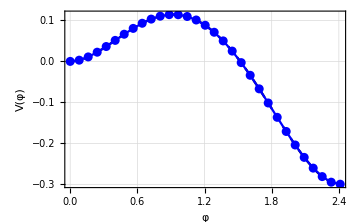
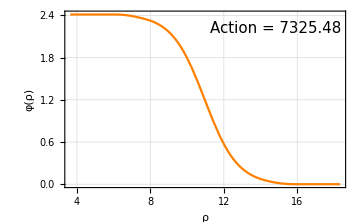

```mathematica
plot1 ={Show[plotU,ListPlot[Transpose@{PB1["Path"],PB1["Potential"]},Joined->True,Mesh->All,PlotStyle->{Blue,PointSize[.018]}]],BouncePlot[PB1,ImageSize->Medium,Epilog->{Text[Style[Row[{"Action = ",PB1["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]}]};
Row[{plot1[[1]],plot1[[2]]}]
```

### ExamplePlot

```mathematica
U[x_]:=.5x^2-.5x^3+.1 x^4;
Extrema=Block[{x},x/.Sort@NSolve[(D[U[x],x])==0,x]];
PB =  FindBounce[ U[x],{x},{Extrema[[1]],Extrema[[3]]}, "Dimension"->3]
BouncePlot[PB,PlotLabel->Row[{"Action: ",PB["Action"]}]]
```

FindBounce[0.5 x^2-0.5 x^3+0.1 x^4,{x},{0.,2.88278},Dimension→3]

BouncePlot[FindBounce[0.5 x^2-0.5 x^3+0.1 x^4,{x},{0.,2.88278},Dimension→3],PlotLabel→Action: FindBounce[0.5 x^2-0.5 x^3+0.1 x^4,{x},{0.,2.88278},Dimension→3][Action]]

```mathematica
(*Export[ FileNameJoin[{FileNameTake[NotebookDirectory[],{1,-2}],"ExaplesBounces1D.png"}],BouncePlot[PB,PlotLabel->Row[{"Action: ",PB["Action"]}]]];*)
```

## Single Field Quartic Potential

### Potential

```mathematica
Module[{ϵ = 1,Vt=5,ϕm=10,Vm=-20,ϕp=-5,Vp,ΔVp,ΔVm,α,Δ,Rt,A},
	Vp = -18+(ϵ-1)*3;
	ΔVm=Vt-Vm;
	ΔVp= Vt - Vp;
	α = -ϕp/ϕm;
	Δ = ΔVp/ΔVm;
	Rt = Sqrt[2 (1 + α)(α+Δ)]/(1 - Δ)ϕm/Sqrt[Vm];
	A = (1 + Sqrt[1 + 2 ΔVp Rt^2/ϕp^2])/( ΔVp Rt^2/ϕp^3);
	Extrema ={ϕp,0,ϕm} ;
	U[ϕ_] :=Piecewise[{{(Vp + ΔVp/ϕp^4 (ϕ-ϕp)^4)-Vp ,ϕ<0},{(Vm+  ΔVm/ϕm^4 (ϕ-ϕm)^4)-Vp,ϕ≥ 0}}];
	ActionExact =((2 π^2 ϕm^4)/(3ΔVm)) (4 α^3 + 6 α^2 Δ + 4α Δ^2+Δ^3+α^4(3+Δ(Δ -3)))/(1 - Δ)^3;
];
plotU = Plot[U[Extrema[[3]]-ϕ],{ϕ,0,Abs@Extrema[[1]]+Abs@Extrema[[3]]},
	PlotStyle->{Black,Dashed},
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False
];
```

### Bounce

```mathematica
PBDefault =  FindBounce[ U[ϕ],{ϕ},{Extrema[[1]],Extrema[[3]]},"InitialLocalMaximum"->Extrema[[2]],"MethodSegmentation"->"2H",Gradient->None]
PB200 =  FindBounce[ U[ϕ],{ϕ},{Extrema[[1]],Extrema[[3]]},"InitialLocalMaximum"->Extrema[[2]],"Segments"->200,"MethodSegmentation"->"2H"]
Row[{"Exact Action = ",N@ActionExact}]
(*"Improvement"->False is needed since the second derivative is not well defined.*)
```

7
BounceFunction[<|Action -> 2.33978 10 , Bounce -> (Piecewise[<<2>>] & ), <<9>>, Radii -> {1.26895, 17.6979, 37.2782, 43.1417, 45.8706, 47.4536, 48.4875, 49.2157, 49.7563, 50.1735, 50.5052, 50.7752, 50.9993, 51.1883, 51.3497, 51.4893, 51.6112, 51.7185, 51.8137, 51.8987, 51.9752, 52.0554, 52.1554, 52.2834, 52.4531, 52.6886, 53.0369, 53.6027, 54.6718, 57.3326, 70.5526}|>]

SingleFieldBounceImprovement::dVFailed: The first derivative of the Potential is not well define at some field value. "Gradient"->None was taken.

7
BounceFunction[<|Action -> 2.27337 10 , <<10>>, Radii -> {0.0254155, 0.0274247, 0.0300006, 0.0334721, 0.0385168, 0.0468485, 0.0649032, 1.04751, 17.9914, 24.4935, 28.6493, 31.6474, 33.9451, 35.775, 37.2725, 38.5236, 39.5861, 40.5007, 41.2968, 41.9964, 42.6162, 43.1695, <<168>>, 55.5884, 56.0853, 56.6992, 57.477, 58.4943, 59.8812, 61.8825, 65.0167, 70.5979, 83.1476, 152.778}|>]

Exact Action = 2.27175×10^7

### Plot

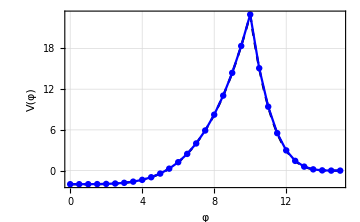
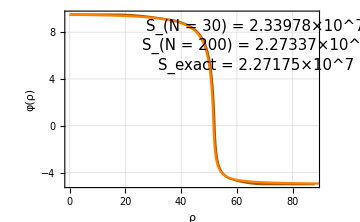

```mathematica
plot1 ={Show[plotU,ListPlot[Transpose@{PBDefault["PathLongitudinal"],PBDefault["Potential"]},Joined->True,Mesh->All,PlotStyle->Blue]],Show[{BouncePlot[PBDefault,PlotStyle->Darker@Orange],BouncePlot[PB200]},ImageSize->Medium,Epilog->{Text[Style[Row[{"S_(N = 30) = ",PBDefault["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.91}],Background->LightGreen],
Text[Style[Row[{"S_(N = 200) = ",PB200["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.8}],Background->LightGreen],
Text[Style[Row[{"S_exact = ",N@ActionExact}],10,15,"Times New Roman"],Scaled[{0.75,0.69}],Background->LightRed]}]};
Row[{plot1[[1]],plot1[[2]]}]
```

## Two Field Potential: Case B

### Potential

```mathematica
μλαϵ={{80.,100.},{.1,.3},2.,{0.,0.}} ;
rangeU={-16000,1000};
Extrema2 = {{0,12.9099},{6.25901,6.00687},{20.,0.}};
Potential2[ϕ_]:=Sum[-μλαϵ[[1,i]] (ϕ[[i]])^2 +μλαϵ[[2,i]](ϕ[[i]])^4+μλαϵ[[4,i]]ϕ[[i]] ,{i,1,2}]+ μλαϵ[[3]](ϕ[[1]])^2 (ϕ[[2]])^2; 
contourV = ContourPlot[ Potential2[{ϕ1,ϕ2}],{ϕ1,-1,21},{ϕ2,-1,Extrema2[[1,2]]+1},
	PlotRange->rangeU,
	ContourShading->None,
	GridLines->Automatic,
	Contours->50,
	GridLinesStyle->Directive[Dashed,GrayLevel[.85]],
	ContourStyle->Opacity[0.4],
	FrameLabel->{"φ_1","φ_2"},
	ImageSize->400,
	LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain] 
];
```

### Bounce

```mathematica
PB2 = FindBounce[Potential2[{φ1,φ2}],{φ1,φ2},{{0.,12.91},{20.,0.}}]
```

Total time consumed = 0.081859 s.

BounceFunction[<|Action -> 4959.39, Bounce -> <<1>>, <<10>>, Radii -> {0.534331, 0.664677, 0.696914, 0.716585, 0.731092, 0.742791, 0.752742, 0.761513, 0.769448, 0.776773, 0.783644, 0.790178, 0.796463, 0.802573, 0.808569, 0.814507, 0.820439, 0.826418, 0.832497, 0.838737, 0.845208, 0.851995, 0.859209, 0.866999, 0.875574, 0.885257, 0.896576, 0.910507, 0.929174, 0.958888, 1.05275}|>]

### Plot

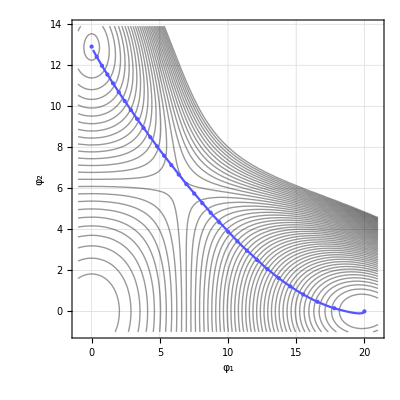
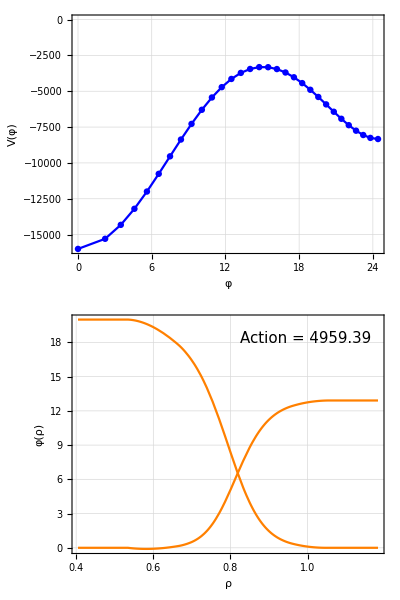

```mathematica
bounce=PB2["Bounce"];
R=PB2["Radii"];
markers=bounce/@R;
pBounce2 =Show[ParametricPlot[bounce[ρ],{ρ,0,1},PlotStyle->Lighter@Blue]];
Potential1D = ListPlot[Transpose@{PB2["PathLongitudinal"],PB2["Potential"]},
	Joined->True,
	Mesh->All,
	PlotStyle->Blue,
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False];
plot2 = {Show[contourV,pBounce2 ,
	PlotRange->All,
	ImageSize->400,
	Epilog->{PointSize[Medium],Lighter@Blue,Point[markers]}
],
	Column[{Potential1D,
	BouncePlot[PB2,ImageSize->Medium,
Epilog->{Text[Style[Row[{"Action = ",PB2["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]}]}
	]};Row[plot2]
```

## Two Field Potential: Case A

### Potential

```mathematica
μλαϵ= {{80.,100.},{.1,.3},2.,{0.,800.}}; 
rangeU={-20000,5000};
Extrema2 = {{0,10.},{2.51278,6.2744397},{19.9166676,-0.5767454}};
Potential2[ϕ_]:=Sum[-μλαϵ[[1,i]] (ϕ[[i]])^2 +μλαϵ[[2,i]](ϕ[[i]])^4+μλαϵ[[4,i]]ϕ[[i]] ,{i,1,2}]+ μλαϵ[[3]](ϕ[[1]])^2 (ϕ[[2]])^2; 
contourV = ContourPlot[ Potential2[{ϕ1,ϕ2}],{ϕ1,-1,21},{ϕ2,-1,Extrema2[[1,2]]+1},
	PlotRange->rangeU,
	ContourShading->None,
	GridLines->Automatic,
	Contours->50,
	GridLinesStyle->Directive[Dashed,GrayLevel[.85]],
	ContourStyle->Opacity[0.4],
	FrameLabel->{"φ_1","φ_2"},
	ImageSize->400,
	LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain] 
];
```

### Bounce

```mathematica
PB2 = FindBounce[Potential2[{φ1,φ2}],{φ1,φ2},Extrema2[[{1,3}]],"Dimension"->3,"Segments"->12];
```

### Plot

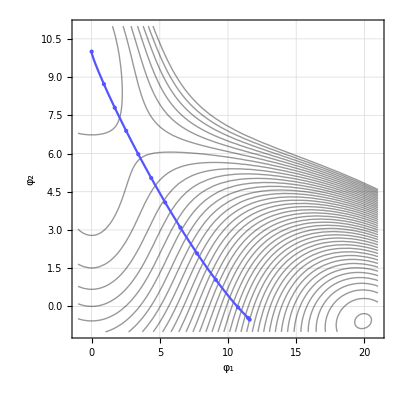
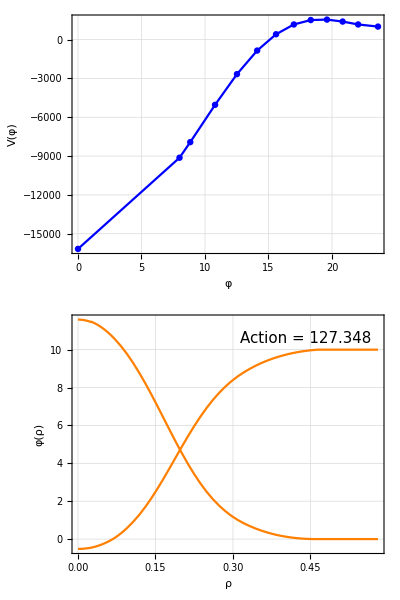

```mathematica
bounce=PB2["Bounce"];
R=PB2["Radii"];
markers=bounce/@R;
pBounce2 =Show[ParametricPlot[bounce[ρ],{ρ,R[[1]],R[[-1]]},PlotStyle->Lighter@Blue]];
Potential1D = ListPlot[Transpose@{PB2["PathLongitudinal"],PB2["Potential"]},
	Joined->True,
	Mesh->All,
	PlotStyle->Blue,
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False];
plot2 = {Show[contourV,pBounce2 ,
	PlotRange->All,
	ImageSize->400,
	Epilog->{PointSize[Medium],Lighter@Blue,Point[markers]}
],
	Column[{Potential1D,
	BouncePlot[PB2,ImageSize->Medium,Epilog->{Text[Style[Row[{"Action = ",PB2["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]}]}]
};Row[plot2]
```

## Three Field Potential

### The Potential

#### Minima

```mathematica
{typeV,Extrema3,parameters3}=Block[{μ1=40,μ2=100,μ3=120,λ1=.1,λ2=.2,λ3=.3,α1=2,α2=2.1,α3=1.2,ϵ1 =100,ϵ2 = 150,ϵ3 = 100,V,Φ,ϕ1,ϕ2,ϕ3,dV,d2V,sols,typeV,Extrema,ExtremaAnsatz,singEig ,parameters3},
V[ϕ_] := -μ1 (ϕ[[1]])^2-μ2 (ϕ[[2]])^2-μ3 (ϕ[[3]])^2 +λ1 (ϕ[[1]])^4+λ2 (ϕ[[2]])^4+λ3 (ϕ[[3]])^4+ α1 (ϕ[[1]])^2 (ϕ[[2]])^2+α2 (ϕ[[1]])^2 (ϕ[[3]])^2+α3 (ϕ[[2]])^2 (ϕ[[3]])^2 +ϵ1 ϕ[[1]] +ϵ2 ϕ[[2]] +ϵ3 ϕ[[3]] ;
Φ = {ϕ1,ϕ2,ϕ3};
dV = D[V[Φ],{Φ}];
d2V = D[V[Φ],{Φ},{Φ}];
ExtremaAnsatz={{0.,-15.8113883,0.},{6.54653671,-5.976143,0.},{20.,0.,0.}};
(*Find new minima*)
sols = Table[FindRoot[dV,Transpose@{Φ,ExtremaAnsatz[[i]]}],{i,1,3}];
d2V = D[V[Φ],{Φ},{Φ}]/.sols;
singEig =Table[DeleteDuplicates@Sign[Eigenvalues@d2V[[i]]],{i,1,3}];
(*Classify type of minima*)
typeV = Table[If[Length@singEig[[i]] >1,"Saddle",If[singEig[[i,1]] >0,"Minimum","Maximum"]],{i,1,3}];
Extrema = Φ/.sols;
parameters3 = {μ1,μ2,μ3,λ1,λ2,λ3,α1,α2,α3,ϵ1,ϵ2,ϵ3} ;
{typeV,Extrema,parameters3}//Chop
];
Row[{"type of Minima: ",typeV}]
```

type of Minima: {Minimum,Saddle,Minimum}

#### Potential

```mathematica
Potential3[ϕ_]:=Block[{V,μ1,μ2,μ3,λ1,λ2,λ3,α1,α2,α3,ϵ1,ϵ2,ϵ3},
{μ1,μ2,μ3,λ1,λ2,λ3,α1,α2,α3,ϵ1,ϵ2,ϵ3}=parameters3;
V = -μ1 (ϕ[[1]])^2-μ2 (ϕ[[2]])^2-μ3 (ϕ[[3]])^2 +λ1 (ϕ[[1]])^4+λ2 (ϕ[[2]])^4+λ3 (ϕ[[3]])^4+ α1 (ϕ[[1]])^2 (ϕ[[2]])^2+α2 (ϕ[[1]])^2 (ϕ[[3]])^2+α3 (ϕ[[2]])^2 (ϕ[[3]])^2 +ϵ1 ϕ[[1]] +ϵ2 ϕ[[2]] +ϵ3 ϕ[[3]] ];
φs3 = {φ1,φ2,φ3};
```

#### Plot

```mathematica
plotPotential =Block[{extremaV,triangleV,potential3,plotZ},
triangleV = Graphics3D[{Darker[Red],Thickness[.005],Line[Extrema3]}];
extremaV=ListPointPlot3D[ Extrema3 ,PlotStyle->{Directive[ Orange,PointSize[.02]]}];
potential3 =Show[RegionPlot3D[Potential3[{Φ1,Φ2,Φ3}]<-1500,{Φ1,-1.5,22},{Φ2,-22,2},{Φ3,-2.8,1},PlotStyle->{Directive[Darker[Orange],Opacity[0.5]],Directive[Lighter[Blue],Opacity[0.5]]},Mesh->None,AxesLabel->{"ϕ_1","ϕ_2","ϕ_3"},LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain],PlotRange->All,Lighting->"Neutral",Background->None],
triangleV,extremaV];

plotZ =Show[ContourPlot[Potential3[{Φ1,Φ2,-2.5}],{Φ1,-1.5,22},{Φ2,-22,2},Contours->60,GridLines->Automatic,Axes->False,GridLinesStyle->Directive[Dashed,GrayLevel[.85]],ContourStyle->Opacity[0.4],ImageSize->Medium,PlotRangePadding->0,Frame->False,LabelStyle->Directive[Black,FontSize->25, FontFamily->"Times New Roman",FontSlant->Plain]],ListPlot[Transpose@Transpose[Extrema3][[{1,2}]],PlotStyle->{Directive[ Orange,PointSize[.02]]}],ListPlot[Transpose@Transpose[Extrema3][[{1,2}]],PlotStyle->{Red},Joined->True]];

{Show[potential3,PlotRange->All,BoxRatios->{1,1,1},ImageSize->400],plotZ } 
];
contourZ[plotZ_Graphics]:=Block[{levelZ,c,projectionZ},
c =PlotRange/.plotZ[[2]];
levelZ=-3.5;
projectionZ=Graphics3D[{Texture[plotZ],EdgeForm[],Polygon[{{c[[1,1]],c[[2,1]],levelZ},{c[[1,2]],c[[2,1]],levelZ},{c[[1,2]],c[[2,2]],levelZ},{c[[1,1]],c[[2,2]],levelZ}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral",ImageSize->400]
];
```

### Bounce

```mathematica
PB3 = FindBounce[Potential3[φs3],φs3,{Extrema3[[1]],Extrema3[[3]]},"InitialLocalMaximum"->Extrema3[[2]]]
```

BounceFunction[<|Action -> 275.433, Bounce -> (<<8>>e[<<2>>] & ), <<10>>, Radii -> {0., 0.129575, 0.185913, 0.213804, 0.233503, 0.249081, 0.262194, 0.273691, 0.284069, 0.293649, 0.302652, 0.311243, 0.319547, 0.32767, 0.335703, 0.34373, 0.351829, 0.360084, 0.36858, 0.37741, 0.386676, 0.39649, 0.406972, 0.418289, 0.430734, 0.44477, 0.46116, 0.481305, 0.508274, 0.551329, 0.704913}|>]

### Plot

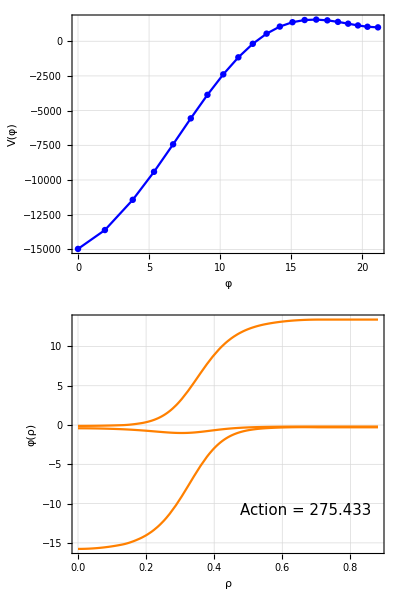
-Graphics3D--Graphics-

```mathematica
pBounce3 = BouncePlot[PB3,ImageSize->Medium,Epilog->{Text[Style[Row[{"Action = ",PB3["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.18}],Background->LightGreen]}];
bounce=PB3["Bounce"];
R=PB3["Radii"];
markers=bounce/@R;
pPathBounce3 =Show[ParametricPlot3D[bounce[ρ],{ρ,0,1},PlotStyle->Cyan]];
PlotBounce2DProjection =Show[ParametricPlot[bounce[ρ][[{1,2}]],{ρ,0,1},PlotStyle->Cyan]];
pPotential1D = ListPlot[Transpose@{PB2["PathLongitudinal"],PB2["Potential"]},
	Joined->True,
	Mesh->All,
	PlotStyle->Blue,
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False];
plot3 = {Show[{plotPotential[[1]],contourZ[Show[plotPotential[[2]],Show[PlotBounce2DProjection]]],pPathBounce3 },
	PlotRange->All,
	ImageSize->400],
Column[{pPotential1D,pBounce3}]};Row[plot3]
```

## All Plots

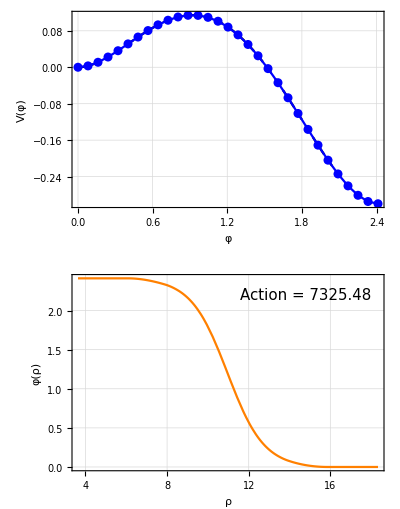
-Graphics--Graphics--Graphics-     -Graphics3D--Graphics-

```mathematica
PLOTS = Magnify[Row[Flatten[{GraphicsGrid[Transpose@{plot1}],plot2,"     ",plot3,"    "}]],.6]
```

```mathematica
(*Export[ FileNameJoin[{FileNameTake[NotebookDirectory[],{1,-2}],"ExaplesBounces.png"}],PLOTS ];*)
```

## Possible Issues

### Accuracy Bounce

FindInitialRadii::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

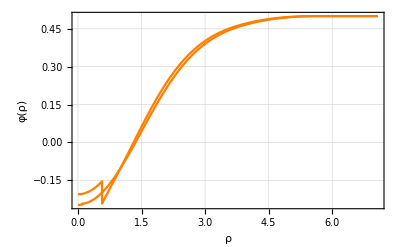

```mathematica
PB1 =FindBounce[x^4-x^2+x/2,x,{-0.809017,0.5},"Dimension"->3];
PB2 = FindBounce[x^4-x^2+x/2,x,{-0.809017,0.5},"Dimension"->3,"AccuracyInitialRadii"->16];
BouncePlot[{PB1,PB2}]
```

### Local Maximum

```mathematica
U1[x_]:=Block[{αs = .4,V},V = 1/2(x)^2-1/2(x)^3+αs/8 (x)^4 ];
Extrema1=Block[{φ},φ/.Sort@NSolve[(D[U1[φ],φ])==0,φ]];
FindBounce[U1[x],x,{Extrema1[[1]],Extrema1[[3]]},"Segments"->2]
FindBounce[U1[x],x,{Extrema1[[1]],Extrema1[[3]]},"Segments"->2,"InitialLocalMaximum"->Extrema1[[2]]]
```

SingleFieldBounce::extrema: Wrong position of the minima.

$Failed

2                              1.87627               2
BounceFunction[<|Action -> 21.6725, Bounce -> (Piecewise[{{1.7575 - 0.566406 #1 , #1 < 1.34056}, {-0.330628 + ------- + 0.0145655 #1 , 1.34056 <= #1 < 3.36893}}] & ), Coefficients -> {{1.7575, -0.330628}, {-0.566406, 0.0145655}, {-0.0000148889, 1.87627}}, Dimension -> 4, Domain -> {0, 3.36893}, <<5>>, Potential -> {-27.1956, 0.0861814, 0.}, Radii -> {0., 1.34056, 3.36893}|>]
                                                                                                                  2
                                                                                                                #1

### Accuracy Minima

```mathematica
FindBounce[.5x^2-.5x^3+.05x^4,x,{0.,6.760398644698},"Dimension"->3]
FindBounce[.5x^2-.5x^3+.05x^4,x,{0.,6.760398644698},"Dimension"->3,"AccuracyInitialRadii"->16]
FindBounce[.5x^2-.5x^3+.05x^4,x,{0.,6.760398644698074},"Dimension"->3,"AccuracyInitialRadii"->16]
```

BounceFunction[<|Action -> 40.6061, Bounce -> (<<1>> & ), <<9>>, Radii -> {0.169782, 0.176137, 0.182985, 0.19038, 0.198389, 0.207086, 0.216558, 0.226906, 0.238248, 0.25072, 0.264486, 0.279736, 0.296696, 0.315636, 0.336876, 0.360802, 0.387877, 0.418664, 0.453848, 0.494276, 0.541006, 0.595385, 0.659182, 0.734802, 0.825685, 0.937075, 1.07768, 1.26372, 1.53129, 1.99092, 3.78171}|>]

BounceFunction[<|Action -> 40.6061, Bounce -> (<<1>> & ), <<9>>, Radii -> {0.169782, 0.176137, 0.182985, 0.19038, 0.198389, 0.207086, 0.216558, 0.226906, 0.238248, 0.25072, 0.264486, 0.279736, 0.296696, 0.315636, 0.336876, 0.360802, 0.387877, 0.418664, 0.453848, 0.494276, 0.541006, 0.595385, 0.659182, 0.734802, 0.825685, 0.937075, 1.07768, 1.26372, 1.53129, 1.99092, 3.78171}|>]

FindInitialRadii::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

BounceFunction[<|Action -> 32.6396, <<10>>, Radii -> {-0.000622137, -0.000661369, -0.000705882, -0.00075682, -0.00081568, -0.000884469, -0.000965928, -0.00106391, -0.00118402, -0.0013347, -0.00152933, -0.0017904, -0.00215896, -0.00271858, -0.00366981, -0.00564482, -0.0122168, 0.110842, <<4>>, 1.33308, 1.50502, 1.68507, 1.88071, 2.10284, 2.37051, 2.72466, 3.28796, 5.20935}|>]

## Dynamical Examples

## Single Field Potential

### Plot

```mathematica
ListPlotBounce[pts_List]:=Block[{PB,φV,plot,mge},
	φV = Transpose[pts];
	PB =FindBounce[Null,Null,{φV[[1,1]],φV[[1,-1]]},"InitialPath"->φV[[1]],"InitialPotential"->φV[[2]],"AccuracyInitialRadii"->8];
	Plot[PB["Bounce"][ρ],{ρ,0,50},
	ImageSize->Medium,
	PlotRange->{{0,50},{-1,6}},
Epilog->{Text[Style[Row[{"Action = ",PB["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.2}],Background->LightGreen]},		
	Frame->True,
		FrameLabel->{"ρ","φ(ρ)"},
		LabelStyle->Directive[Black,FontSize->17, 
FontFamily->"Times New Roman",FontSlant->Plain],
		GridLines->Automatic,
		PlotStyle->Orange]  ];
DynamicModule[{pts ={{1,0},{2,2},{3,2.55},{4,2},{5,1}},d=4,ptsT,PB,plot},
ptsT =Transpose[pts];
Row[{LocatorPane[Dynamic[pts],Dynamic[   ListPlot[pts,Joined->True,Mesh->All,PlotRange->{{-1,6},{Min[ptsT[[2]]] 1.5-2,Max[ptsT[[2]]]1.5}},Frame->True,
FrameLabel->{"φ","V(φ)"},GridLines->Automatic,GridLinesStyle->GrayLevel[.85],ImageSize->Medium,MeshStyle->PointSize[Large],LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],PlotStyle->Darker[Blue],Axes->False]      ],Appearance->None],Dynamic[ListPlotBounce[pts]] }]]
```

## Two Field Potential

### Plot

```mathematica
DynamicModule[{μ,λ,αs,ϵ,μλαϵ,Extrema,plot,abort,Action,Potential2,dV,d2V,plots,ϕ1,ϕ2,ϕs,d=4,PB2 ,plot2,pBounce2,Potential1D,pPathBounce2,Extrema0={{0,12.9099},{6.259,6.00687},{20.,0.}}},
Manipulate[
 μλαϵ={{μ1,μ2},{λ1,λ2},α,{ϵ1,ϵ2}};
(*========================================*)
Potential2[ϕ_]:=μλαϵ⟦3⟧ ϕ⟦1⟧^2 ϕ⟦2⟧^2-ϕ⟦1⟧^2 μλαϵ⟦1,1⟧-ϕ⟦2⟧^2 μλαϵ⟦1,2⟧+ϕ⟦1⟧^4 μλαϵ⟦2,1⟧+ϕ⟦2⟧^4 μλαϵ⟦2,2⟧+ϕ⟦1⟧ μλαϵ⟦4,1⟧+ϕ⟦2⟧ μλαϵ⟦4,2⟧; 
dV[ϕ_]:= {2 μλαϵ⟦3⟧ ϕ⟦1⟧ ϕ⟦2⟧^2-2 ϕ⟦1⟧ μλαϵ⟦1,1⟧+4 ϕ⟦1⟧^3 μλαϵ⟦2,1⟧+μλαϵ⟦4,1⟧,2 μλαϵ⟦3⟧ ϕ⟦1⟧^2 ϕ⟦2⟧-2 ϕ⟦2⟧ μλαϵ⟦1,2⟧+4 ϕ⟦2⟧^3 μλαϵ⟦2,2⟧+μλαϵ⟦4,2⟧};
d2V[ϕ_]:= {{2 μλαϵ⟦3⟧ ϕ⟦2⟧^2-2 μλαϵ⟦1,1⟧+12 ϕ⟦1⟧^2 μλαϵ⟦2,1⟧,4 μλαϵ⟦3⟧ ϕ⟦1⟧ ϕ⟦2⟧},{4 μλαϵ⟦3⟧ ϕ⟦1⟧ ϕ⟦2⟧,2 μλαϵ⟦3⟧ ϕ⟦1⟧^2-2 μλαϵ⟦1,2⟧+12 ϕ⟦2⟧^2 μλαϵ⟦2,2⟧}};
ϕs ={ϕ1,ϕ2};
(*========================================*) 
Quiet[Extrema = Table[ϕs/.Chop@FindRoot[dV[ϕs],Transpose@{ϕs,Extrema0[[i]]}],{i,3}];
PB2  = FindBounce[Potential2[ϕs],ϕs,Extrema[[{1,3}]],"InitialLocalMaximum"->Extrema[[2]], "Dimension"->d, "Segments"->n,"MaxIterationsPath"->2,Gradient->dV[ϕs],Hessian->d2V[ϕs]];
pBounce2 = BouncePlot[PB2["Bounce"],ImageSize->Medium]; 
pPathBounce2 =ParametricPlot[PB2["Bounce"][ρ],{ρ,0,10},PlotStyle->Cyan];
Potential1D = ListPlot[Transpose@{PB2["PathLongitudinal"],PB2["Potential"]},
	Joined->True,
	Mesh->All,
	PlotStyle->Blue,
	Frame->True,
	FrameLabel->{"φ","V(φ)"},
	LabelStyle->Directive[Black,FontSize->17, FontFamily->"Times New Roman",FontSlant->Plain],
	GridLines->Automatic,
	GridLinesStyle->GrayLevel[.85],	
	ImageSize->Medium,	
	PlotRange->All,
	Axes->False];
(*========================================*) 
plots =Show[ ContourPlot[ Potential2[{ϕ1,ϕ2}],{ϕ1,-5,25},{ϕ2,-5,25},PlotRange->{Automatic,5000},GridLines->Automatic,Contours->10,GridLinesStyle->Directive[Dashed,GrayLevel[.85]],ContourStyle->Opacity[0.4],FrameLabel->{"φ_1","φ_2"},LabelStyle->Directive[Black,FontSize->20, FontFamily->"Times New Roman",FontSlant->Plain],PlotPoints->2,MaxRecursion->3] , ListPlot[ Extrema ,PlotStyle->{PointSize[.015],Darker@Red} ],pPathBounce2];     ];
(*========================================*) 
Row[{Show[plots,ImageSize->Medium],Column[{Potential1D,BouncePlot[PB2,ImageSize->Medium,Epilog->{Text[Style[Row[{"Action = ",PB2["Action"]}],10,15,"Times New Roman"],Scaled[{0.75,0.9}],Background->LightGreen]}]}]}]
,{{μ1,80.,"μ_1"},70,120,Appearance->"Labeled"},{{μ2,100.,"μ_2"},70,120,Appearance->"Labeled"},{{λ1,.1,"λ_1"},.05,.8,Appearance->"Labeled"},{{λ2,.2,"λ_2"},.05,.8,Appearance->"Labeled"},{{α,3.,"α"},0.7,8,Appearance->"Labeled"},{{ϵ1,0,"ϵ_1"},0,800,Appearance->"Labeled"},{{ϵ2,0.,"ϵ_2"},0,800,Appearance->"Labeled"},{{n,20,"n"},10,30,1,Appearance->"Labeled"},Paneled->False ]]
```

## Physical Examples

## DecayRate: Disappearing Instanton

### δV3

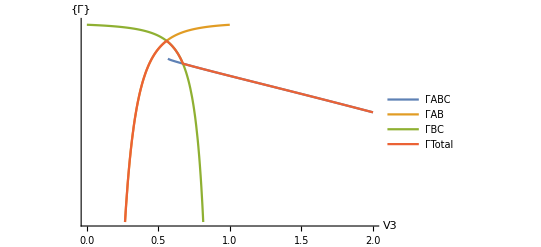

```mathematica
DecayRateV3 = Quiet@Module[{initialPotential,initialPath ,ΓABC,ΓAB,ΓBC,ΓTotal},
initialPotential[V3_]:= {0,2,V3,2,1};
initialPath = {0,1,2,3,4};
ΓABC[V3_]:= 
SetPrecision[Exp[-SetPrecision[FindBounce[Null,Null, initialPath[[{1,-1}]],
"InitialPath"->initialPath,"InitialPotential"->initialPotential[V3]]["Action"],15]],15] ;

ΓAB[V3_]:=If[V3<.999&&V3>0.001,
SetPrecision[Exp[-SetPrecision[FindBounce[Null,Null, {initialPath[[1]],initialPath[[3]]},"InitialPath"->initialPath[[1;;3]],"InitialPotential"->(initialPotential[V3][[1;;3]]) ]["Action"],15]],15],$Failed["Action"]];

ΓBC[V3_]:=If[V3<.999,
SetPrecision[Exp[-SetPrecision[FindBounce[Null,Null,{initialPath[[3]],initialPath[[-1]]},"InitialPath"->initialPath[[3;;5]],"InitialPotential"->initialPotential[V3][[3;;5]]]["Action"],15]],15],$Failed["Action"]];

ΓTotal[V3_]:=If[NumericQ[ΓABC[V3]],ΓABC[V3],0]+If[NumericQ[ΓAB[V3]]&&NumericQ[ΓBC[V3]],ΓAB[V3]*ΓBC[V3]/(ΓAB[V3]+ΓBC[V3]),0];

LogPlot[{ΓABC[V3],ΓAB[V3],ΓBC[V3] ,ΓTotal[V3]},{V3,0,2},
PlotLegends->Placed[LineLegend[{"ΓABC","ΓAB","ΓBC","ΓTotal"},LegendFunction->(Framed[#,RoundingRadius->5,Background->White]&),LegendMargins->5],{Right,Center}],
AxesLabel->{"V3","{Γ}"}]
]
```

```mathematica
Manipulate[ListPlot[Transpose[{{0,1,2,3,4},{0,2,V3,2,1}}],PlotRange->{{0,4},Automatic},Joined->True,Mesh->All,AxesLabel->{"Δφ","V"}],{{V3,1},0,3}]
```

### δφ3

```mathematica
Manipulate[ListPlot[Transpose[{{0,1,2+Δφ/2,3,4},{0,2,.6,2,1}}],PlotRange->{{0,4},Automatic},Joined->True,Mesh->All,AxesLabel->{"Δφ","V"}],{{Δφ,0},-2,2}]
```

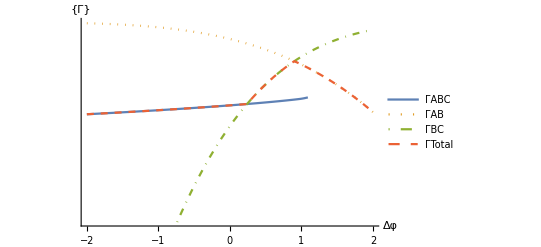

```mathematica
DecayRateΔφ2 = Quiet@Module[{initialPotential,initialPath ,ΓABC,ΓAB,ΓBC,ΓTotal},
initialPotential= {0,2,.7,2,1};
initialPath[Δφ_]:={0,1,2+Δφ/2,3,4};
ΓABC[Δφ_]:= 
SetPrecision[Exp[-SetPrecision[FindBounce[Null,Null, initialPath[Δφ][[{1,-1}]],
"InitialPath"->initialPath[Δφ],"InitialPotential"->initialPotential]["Action"],15]],15] ;

ΓAB[Δφ_]:=
SetPrecision[Exp[-SetPrecision[FindBounce[Null,Null, {initialPath[Δφ][[1]],initialPath[Δφ][[3]]},"InitialPath"->initialPath[Δφ][[1;;3]],"InitialPotential"->(initialPotential[[1;;3]]) ]["Action"],15]],15];

ΓBC[Δφ_]:=
SetPrecision[Exp[-SetPrecision[FindBounce[Null,Null,{initialPath[Δφ][[3]],initialPath[Δφ][[-1]]},"InitialPath"->initialPath[Δφ][[3;;5]],"InitialPotential"->initialPotential[[3;;5]]]["Action"],15]],15];

ΓTotal[Δφ_]:=If[NumericQ[ΓABC[Δφ]],ΓABC[Δφ],0]+If[NumericQ[ΓAB[Δφ]]&&NumericQ[ΓBC[Δφ]],ΓAB[Δφ]*ΓBC[Δφ]/(ΓAB[Δφ]+ΓBC[Δφ]),0];

LogPlot[{ΓABC[Δφ] ,ΓAB[Δφ],ΓBC[Δφ],ΓTotal[Δφ]},{Δφ,-2,2},PlotStyle->{Automatic,Dotted,DotDashed,Dashed},
PlotLegends->Placed[LineLegend[{"ΓABC","ΓAB","ΓBC","ΓTotal"},LegendFunction->(Framed[#,RoundingRadius->5,Background->White]&),LegendMargins->5],{Left,Center}],
AxesLabel->{"Δφ","{Γ}"}]
]
```

### δΔφ

```mathematica
Manipulate[ListPlot[Transpose[{{0,1,2+Δφ/2,3+Δφ,4+Δφ},{0,2,.6,2,1}}],PlotRange->{{0,6},Automatic},Joined->True,Mesh->All,AxesLabel->{"Δφ","V"}],{{Δφ,0},-2,2}]
```

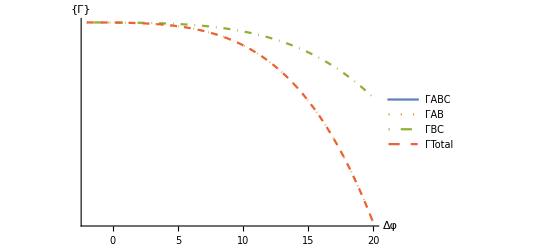

```mathematica
DecayRateΔφ2 = Quiet@Module[{initialPotential,initialPath ,ΓABC,ΓAB,ΓBC,ΓTotal},
initialPotential= {0,2,.5,2,1};
initialPath[Δφ_]:={0,1,2+Δφ/2,3+Δφ,4+Δφ};
ΓABC[Δφ_]:= 
SetPrecision[Exp[-SetPrecision[FindBounce[Null,Null, initialPath[Δφ][[{1,-1}]],
"InitialPath"->initialPath[Δφ],"InitialPotential"->initialPotential]["Action"],15]],15] ;

ΓAB[Δφ_]:=
SetPrecision[Exp[-SetPrecision[FindBounce[Null,Null, {initialPath[Δφ][[1]],initialPath[Δφ][[3]]},"InitialPath"->initialPath[Δφ][[1;;3]],"InitialPotential"->(initialPotential[[1;;3]]) ]["Action"],15]],15];

ΓBC[Δφ_]:=
SetPrecision[Exp[-SetPrecision[FindBounce[Null,Null,{initialPath[Δφ][[3]],initialPath[Δφ][[-1]]},"InitialPath"->initialPath[Δφ][[3;;5]],"InitialPotential"->initialPotential[[3;;5]]]["Action"],15]],15];

ΓTotal[Δφ_]:=If[NumericQ[ΓABC[Δφ]],ΓABC[Δφ],0]+If[NumericQ[ΓAB[Δφ]]&&NumericQ[ΓBC[Δφ]],ΓAB[Δφ]*ΓBC[Δφ]/(ΓAB[Δφ]+ΓBC[Δφ]),0];

LogPlot[{ΓABC[Δφ] ,ΓAB[Δφ],ΓBC[Δφ],ΓTotal[Δφ]},{Δφ,-2,20},PlotStyle->{Automatic,Dotted,DotDashed,Dashed},
PlotLegends->Placed[LineLegend[{"ΓABC","ΓAB","ΓBC","ΓTotal"},LegendFunction->(Framed[#,RoundingRadius->5,Background->White]&),LegendMargins->5],{Left,Center}],
AxesLabel->{"Δφ","{Γ}"}]
]
```

### δV3 + δΔφ

```mathematica
Manipulate[ListPlot[Transpose[{{0,1,2+Δφ/2,3+Δφ,4+Δφ},{0,2,V3,2,1}}],PlotRange->{{0,4},Automatic},Joined->True,Mesh->All,AxesLabel->{"Δφ","V"}],{{Δφ,0},-2,2},{{V3,1},0,3}]
```

```mathematica
DecayRate2D = Quiet@Module[{initialPotential,initialPath ,ΓABC,ΓAB,ΓBC,ΓTotal},
initialPotential[V3_]:= {0,2,V3,2,1};
initialPath[Δφ_]:={0,1,2+Δφ/2,3+Δφ,4+Δφ};
ΓABC[Δφ_,V3_]:= 
SetPrecision[Exp[-SetPrecision[FindBounce[Null,Null, initialPath[Δφ][[{1,-1}]],
"InitialPath"->initialPath[Δφ],"InitialPotential"->initialPotential[V3]]["Action"],15]],15] ;

ΓAB[Δφ_,V3_]:=If[V3<.999&&V3>0.1,
SetPrecision[Exp[-SetPrecision[FindBounce[Null,Null, {initialPath[Δφ][[1]],initialPath[Δφ][[3]]},"InitialPath"->initialPath[Δφ][[1;;3]],"InitialPotential"->(initialPotential[V3][[1;;3]]) ]["Action"],15]],15],$Failed["Action"]];

ΓBC[Δφ_,V3_]:=If[V3<.999,
SetPrecision[Exp[-SetPrecision[FindBounce[Null,Null,{initialPath[Δφ][[3]],initialPath[Δφ][[-1]]},"InitialPath"->initialPath[Δφ][[3;;5]],"InitialPotential"->initialPotential[V3][[3;;5]]]["Action"],15]],15],$Failed["Action"]];

ΓTotal[Δφ_,V3_]:=If[NumericQ[ΓABC[Δφ,V3]],ΓABC[Δφ,V3],0]+If[NumericQ[ΓAB[Δφ,V3]]&&NumericQ[ΓBC[Δφ,V3]],ΓAB[Δφ,V3]*ΓBC[Δφ,V3]/(ΓAB[Δφ,V3]+ΓBC[Δφ,V3]),0];

Plot3D[{Log@ΓTotal[Δφ,V3]},{Δφ,-1.99,2},{V3,0.01,2},PlotLabels->"Log[ΓTotal]",AxesLabel->Automatic]
]
```

-Graphics3D-